# Prodaja kmetijskih pridelkov iz lastne pridelave na živilskih trgih, Slovenija, letno

```mathematica
leta=Range[2000,2021]
```

{2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021}

```mathematica
podatki = Import["\\Users\\hanaa\\Desktop\\Faks\\Računalniška orodja v matematiki\\Podatki projektna Rom.csv","Table","FieldSeparators"->";",CharacterEncoding->"WindowsEastEurope",HeaderLines->1]//Transpose//ResourceFunction["DatasetWithHeaders"]//Map[If[#=="-",0,#]&,#,{2}]&
```

## Količina kmetijskih pridelkov

```mathematica
kolicina=Take[podatki,{1,43,2}];
```

```mathematica
kolicinaLeta=kolicina//Transpose//Prepend["Leta"->leta]//Transpose
```

## Povprečna cena kmetijskih pridelkov

```mathematica
povprecnaCena=Take[podatki,{2,44,2}];
```

```mathematica
povprecnaCenaLeta=povprecnaCena//Transpose//Prepend["Leta"->leta]//Transpose
```

## Vrednost prodanih pridelkov in proizvodov

```mathematica
(*def.: vrednost prodanih pridelkov in proizvodov je količina prodanih pridelkov in proizvodov, pomnožena s povprečno ceno.*)
```

### Vrednost krompirja skozi leta

```mathematica
kolicinaKrompirja=kolicina[All,"Krompir, jedilni (zgodnji in pozni) (kg)"]//Normal;
```

```mathematica
povprecnaCenaKrompirja=povprecnaCena[All,"Krompir, jedilni (zgodnji in pozni) (kg)"]//Normal;
```

```mathematica
vrednostKrompirja = IntegerPart[kolicinaKrompirja * povprecnaCenaKrompirja]
```

{533098,608526,490459,607259,569324,419346,454704,851998,878514,755788,673856,782450,687372,483413,427951,326194,412963,438996,452198,513766,436021,514154}

```mathematica
vTabelo=AssociationThread[ToString/@{"Vrednost krompirja"}->#]&/@vrednostKrompirja;
```

```mathematica
tabelaKrompirja=Dataset[vTabelo]//Transpose//Prepend["Leto"->leta]//Transpose
```

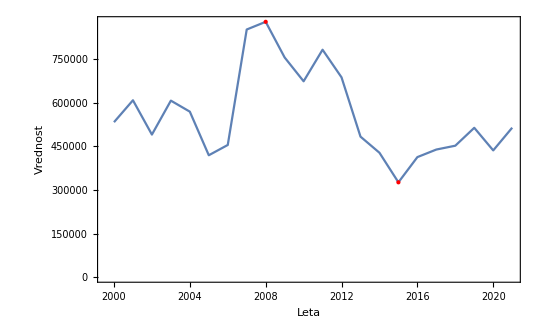

```mathematica
ListLinePlot[tabelaKrompirja,Epilog->{Red,PointSize@Large,Point[{{2008,878514},{2015,326194}}]},Frame->True,FrameLabel->{{"Vrednost",""},{"Leta","Vrednost krompirja"}},BaseStyle->{FontSize->15},BaseStyle->{FontSize->15}]
```

```mathematica
samoVrednostiKrompirja=tabelaKrompirja//Query[All,{2}];
```

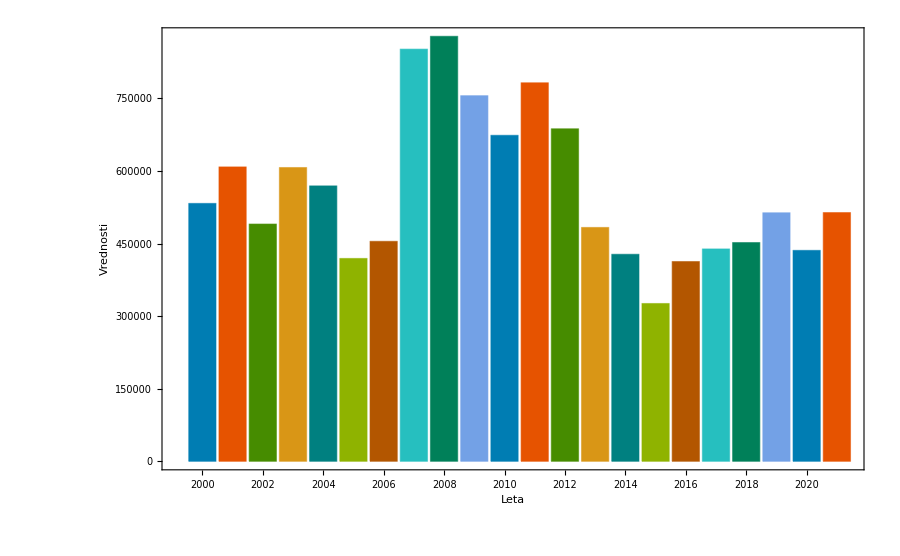

```mathematica
BarChart[Transpose[samoVrednostiKrompirja],ChartLabels->leta,ChartStyle->68,Frame->True,FrameLabel->{{"Vrednosti",""},{"Leta","Vrednost krompirja"}},BaseStyle->{FontSize->14},ImageSize->900]
```

### Vrednost svežega mleka skozi leta

```mathematica
kolicinaMleka=kolicina[All,"Sveže mleko (l)"]//Normal;
```

```mathematica
povprecnaCenaMleka=povprecnaCena[All,"Sveže mleko (l)"]//Normal;
```

```mathematica
vrednostMleka = IntegerPart[kolicinaMleka * povprecnaCenaMleka]
```

{1512,1047,410,210,465,1280,1833,1977,1420,6980,25774,29655,27779,36966,31855,53875,53541,57628,72257,73113,54251,62712}

```mathematica
vTabelo2=AssociationThread[ToString/@{"Vrednost svežega mleka"}->#]&/@vrednostMleka;
```

```mathematica
tabelaMleka=Dataset[vTabelo2]//Transpose//Prepend["Leto"->leta]//Transpose
```

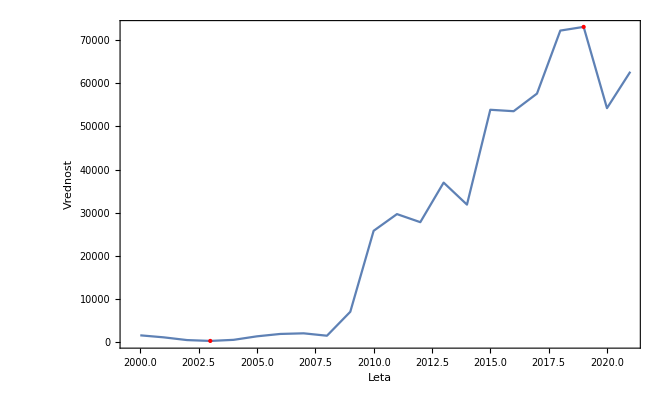

```mathematica
ListLinePlot[tabelaMleka,Epilog->{Red,PointSize@Large,Point[{{2003,210},{2019,73113}}]},Frame->True,FrameLabel->{{"Vrednost",""},{"Leta","Vrednost svežega mleka"}},BaseStyle->{FontSize->15},BaseStyle->{FontSize->15}]
```

```mathematica
samoVrednostiMleka=tabelaMleka//Query[All,{2}];
```

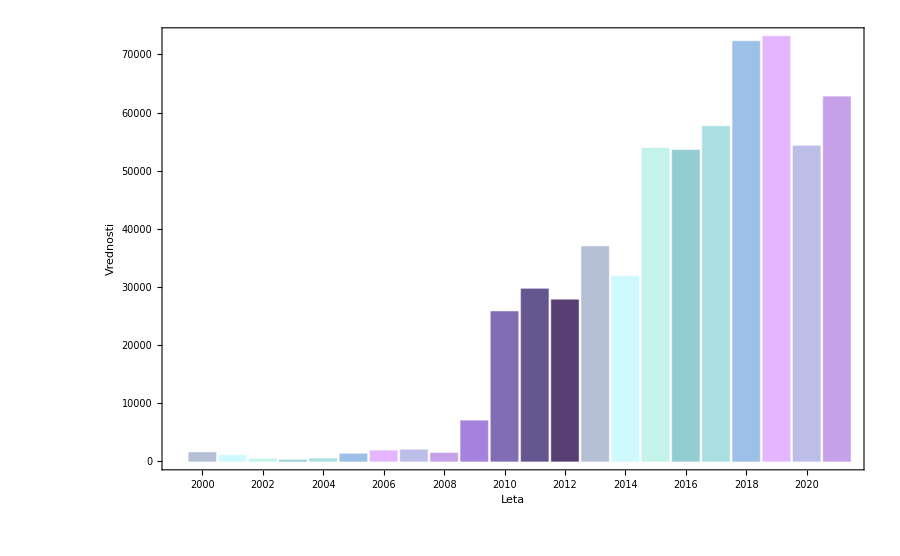

```mathematica
BarChart[Transpose[samoVrednostiMleka],ChartLabels->leta,ChartStyle->55,Frame->True,FrameLabel->{{"Vrednosti",""},{"Leta","Vrednost svežega mleka"}},BaseStyle->{FontSize->14},ImageSize->900]
```

### Vrednost pšenične moke skozi leta

```mathematica
kolicinaMoke=kolicina[All,"Pšenična moka (kg)"]//Normal;
```

```mathematica
povprecnaCenaMoke=povprecnaCena[All,"Pšenična moka (kg)"]//Normal;
```

```mathematica
vrednostMoke = IntegerPart[kolicinaMoke * povprecnaCenaMoke]
```

{24757,16895,20579,16212,16654,36130,45271,43649,29771,21118,17923,19117,15562,28200,17309,12606,13457,13417,23117,34337,13751,19768}

```mathematica
vTabelo3=AssociationThread[ToString/@{"Vrednost pšenične moke"}->#]&/@vrednostMoke;
```

```mathematica
tabelaMoke=Dataset[vTabelo3]//Transpose//Prepend["Leto"->leta]//Transpose
```

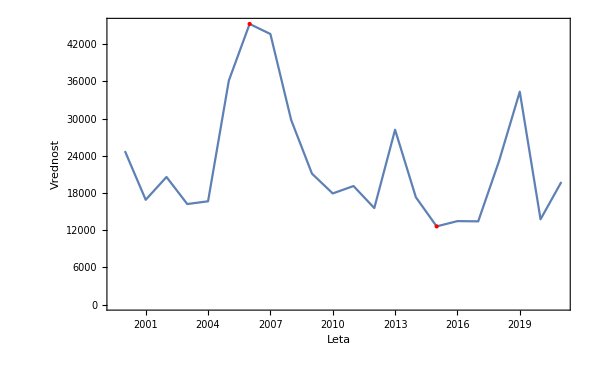

```mathematica
ListLinePlot[tabelaMoke,Epilog->{Red,PointSize@Large,Point[{{2015,12606},{2006,45271}}]},Frame->True,FrameLabel->{{"Vrednost",""},{"Leta","Vrednost pšenične moke"}},BaseStyle->{FontSize->15},BaseStyle->{FontSize->15}]
```

```mathematica
samoVrednostiMoke=tabelaMoke//Query[All,{2}];
```

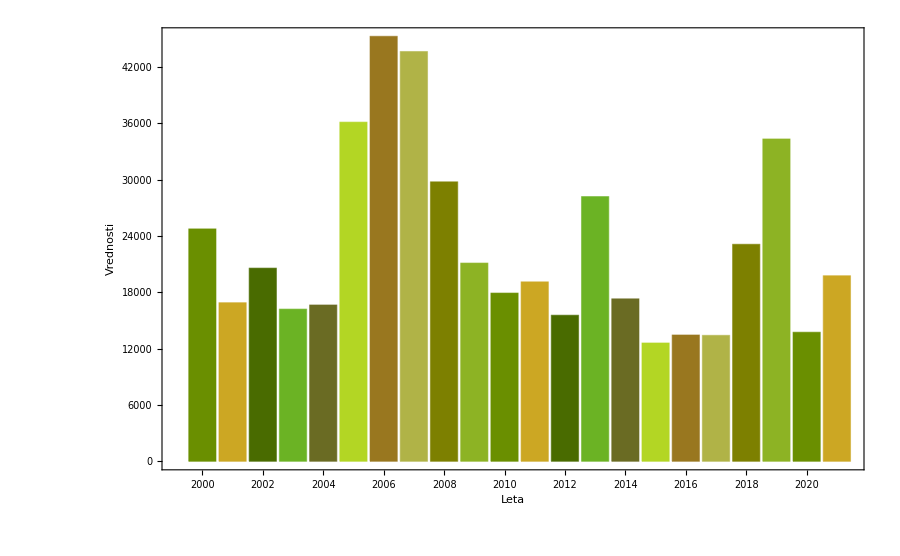

```mathematica
BarChart[Transpose[samoVrednostiMoke],ChartLabels->leta,ChartStyle->78,Frame->True,FrameLabel->{{"Vrednosti",""},{"Leta","Vrednost pšenične moke"}},BaseStyle->{FontSize->14},ImageSize->900]
```